```mathematica
(*Exercício 1*)
```

```mathematica
f[a_][x_]:=a Sin[π x];
```

```mathematica
NestList[f[a],x,2][[3]]
```

a Sin[a π Sin[π x]]

```mathematica
g[a_][x_]:=NestList[f[a],x,2][[3]](*defino uma função auxiliar g = f(f(x))*)
```

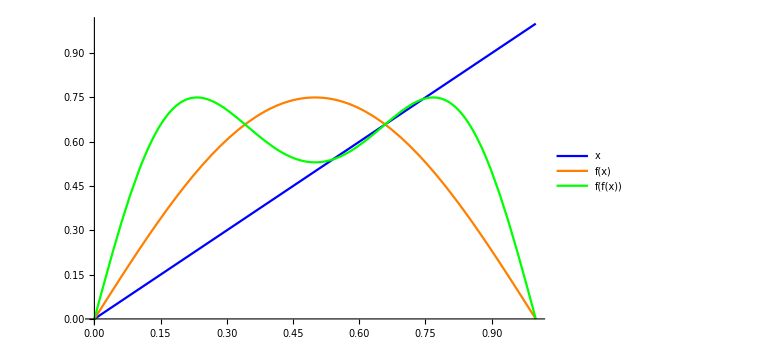

```mathematica
optam={ImageSize->Large,LabelStyle-> {"Large"}};
Plot[{x,f[0.75][x],g[0.75][x]},{x,0,1},Evaluate[optam],PlotStyle->{Blue, Orange, Green},PlotLegends->{"x","f(x)","f(f(x))"}]
```

Observando o gráfico anterior, podemos identificar claramente a presença de um ponto fixo em x = 0 (trivial) e outro ponto fixo em (aproximadamente) x = 0.65. Obtenho esse ponto fixo de maneira exata com base em uma solução numérica da equação f(x) = x.

```mathematica
sol1=NSolve[x==f[0.75][x],x, PositiveReals]
```

{{x→0.6587}}

Resultado perfeitamente consistente com a estimativa feita.

Ainda de acordo com o gráfico construído, é possível identificar outros dois pontos específicos para os quais as curvas azul e verde se intersectam, ou seja, pontos nos quais x = f(f(x)). Pontos com essa característica representam um ciclo 2 ao longo do processo de iteração de f. Tento obtê-los partindo de uma solução numérica da equação x = f(f(x))

```mathematica
sol2=NSolve[x==g[0.75][x],x,PositiveReals]
```

{{x→0.540177},{x→0.6587},{x→0.744034}}

Com exceção do ponto x = 0.6587 (o qual já sabemos que é um ponto fixo de f(x) ), obtivemos duas novas soluções: x = 0.540177 e x = 0.744034. Essas duas soluções representam um ciclo 2 e estão completamente consistentes com as coordenadas obtidas anteriormente.

```mathematica
(*Exercício 2*)
```

```mathematica
(*Começo definindo as funções principais associadas à construção do mapa de bifurcações*)
(*1) Função que produz uma lista de n iterações do mapa, começando do ponto x0 e eliminando os primeiros m elementos*)

(*itera[λ_,m_,n_]:=Drop[NestList[f[λ],0.5,n],m+1] ;*)
itera:=Compile[{a,{m,_Integer},{n,_Integer}},
Drop[NestList[a *Sin[π #]&,0.5,n],m+1]
];

(* 2) Função que produz um ponto cuja abcissa é definida pelo valor de 'a' e cuja ordenada indica um elemento da lista de valores de x*)
ponto[x_]:=Point[{a,x}];
(* 3) Função que varre um número Subscript[n, a] de valores de a entre Subscript[a, min] e Subscript[a, max].*)
graflambda[amin_,amax_,na_,m_,n_]:=Graphics[{PointSize[0.001], Table[Map[ponto,itera[a,m,n]],{a,amin,amax,(amax-amin)/na}]}];
```

```mathematica
(*Faço o plot do gráfico de bifurcações*)
grafico1 =Show[graflambda[0,1,1000,1024,2048],Evaluate[optam],Axes->False,Frame->True,FrameLabel->{"a","x"},PlotRange->{0,1},AspectRatio->1];
Export["BifurcacaoSeno1.png",grafico1];
Clear[grafico1];
Import["BifurcacaoSeno1.png"]
```

-Graphics-

De acordo com os resultados obtidos no item anterior, vimos que para a=0.75 haviam 2 pontos fixos (isto é, um ciclo 2) nos pontos x =0.540177  e x=0.744034, além claro do ponto fixo x =0.6587, o qual já sabíamos estar associado a um ciclo 1. Fazendo uma verificação rápida do mapa anterior com o auxílio da ferramenta GetCoordinates, para a =0.75 temos as seguintes coordenadas:

```mathematica
coordenadas={{"0.7514","0.5409"},{"0.7514","0.7468"}};
```

E, portanto, temos como pontos fixos x=0.5409  e x=0.7468 (aproximadamente). Este resultado indica que o mapa de bifurcações encontrado está em perfeito acordo com as estimativas feitas anteriormente.

```mathematica
(*Exercício 3*)
(*Utilizo a função FindRoot para encontrar os valores de 'a' para os quais o ciclo 2 se desenvolve a um ciclo 4, ciclo 4 se desenvolve a um ciclo 8, e assim sucessivamente. Antes de aplicar esse procedimento, construo mapas de bifurcação ampliados nas regiões próximas às zonas de instabilidade para obter um bom palpite inicial dos parâmetros de interesse.*)
```

```mathematica
solPeriodo1=FindRoot[{Nest[f[a],x,1]==x,D[Nest[f[a],x,1],x]==-1},{{x,0.5},{a,0.3} }]
```

{x→0.645774,a→0.719962}

```mathematica
graficoAux =Show[graflambda[0.83,0.84,1000,1024,2048],Evaluate[optam],Axes->False,Frame->True,FrameLabel->{"a","x"},PlotRange->{0.35,0.85},AspectRatio->1];
Export["Auxiliar.png",graficoAux];
Clear[graficoAux];
Import["Auxiliar.png"]
```

-Graphics-

```mathematica
solPeriodo2=FindRoot[{Nest[f[a],x,2]==x,D[Nest[f[a],x,2],x]==-1},{{x,0.5},{a,0.8} }]
```

{x→0.444794,a→0.833266}

```mathematica
graficoAux =Show[graflambda[0.857,0.865,1000,1024,2048],Evaluate[optam],Axes->False,Frame->True,FrameLabel->{"a","x"},PlotRange->{0.35,0.88},AspectRatio->1];
Export["Auxiliar.png",graficoAux];
Clear[graficoAux];
Import["Auxiliar.png"]
```

-Graphics-

```mathematica
solPeriodo4=FindRoot[{Nest[f[a],x,4]==x,D[Nest[f[a],x,4],x]==-1},{{x,0.8},{a,0.858} }]
```

{x→0.792078,a→0.858609}

```mathematica
solPeriodo8=FindRoot[{Nest[f[a],x,8]==x,D[Nest[f[a],x,8],x]==-1},{{x,0.8},{a,0.864} }]
```

{x→0.80749,a→0.864084}

```mathematica
solPeriodo16=FindRoot[{Nest[f[a],x,16]==x,D[Nest[f[a],x,16],x]==-1},{{x,0.8},{a,0.86} }]
```

{x→0.812838,a→0.865259}

```mathematica
solPeriodo32=FindRoot[{Nest[f[a],x,32]==x,D[Nest[f[a],x,32],x]==-1},{{x,0.815},{a,0.8635} }]
```

{x→0.818447,a→0.866709}

```mathematica
solPeriodo64=FindRoot[{Nest[f[a],x,64]== x,D[Nest[f[a],x,64],x]==-1},{{x,0.8},{a,0.86677} }]
```

{x→0.800055,a→0.866762}

```mathematica
solPeriodo128=FindRoot[{Nest[f[a],x,128]==x,D[Nest[f[a],x,128],x]==-1},{{x,0.817},{a,0.86677} }]
```

{x→0.81692,a→0.866676}

```mathematica
(*Exercício 4*)
```

```mathematica
(*Construo uma tabela com os valores do parâmetro 'a' obtidos no item anterior e o período correspondente.*)
ListaValores={{1,a/.solPeriodo1[[2]]},{2,a/.solPeriodo2[[2]]},{4,a/.solPeriodo4[[2]]},{8,a/.solPeriodo8[[2]]},{16,a/.solPeriodo16[[2]]},{32,a/.solPeriodo32[[2]]},{64,a/.solPeriodo64[[2]]},{128,a/.solPeriodo128[[2]]}}
```

{{1,0.719962},{2,0.833266},{4,0.858609},{8,0.864084},{16,0.865259},{32,0.866709},{64,0.865565},{128,0.866676}}

```mathematica
(*Uma vez definida a lista anterior, construo a lista com estimativas da constante de δ de Feigenbaum*)
delta1=(ListaValores[[2,2]]-ListaValores[[1,2]])/(ListaValores[[3,2]]-ListaValores[[2,2]]);
FeigenbaumDelta={};
AppendTo[FeigenbaumDelta,Subscript[δ, 1]-> delta1];
Do[AppendTo[FeigenbaumDelta,Subscript[δ, i]-> (ListaValores[[i,2]]-ListaValores[[i-1,2]])/(ListaValores[[i+1,2]]-ListaValores[[i,2]])],{i,2,7}];
SetPrecision[FeigenbaumDelta,6]
```

{δ_1→4.4709,δ_2→4.4709,δ_3→4.62871,δ_4→4.66052,δ_5→0.810274,δ_6→-1.26709,δ_7→-1.02992}

```mathematica
(*Até Subscript[δ, 4] as estimativas obtidas parecem sim tender ao valor esperado Subscript[δ, Log]. Entretanto, as estimativas Subscript[δ, 5] em diante divergem completamente do resultado esperado. Isso se deve às dificuldades de obtenção de soluções convergentes na análise dos pontos fixos de ciclo 64 e 128.*)
```

```mathematica
(*Exercício 5*)
```

```mathematica
(*Começo redefinindo a lista FeigenbaumDelta, com elementos entre 3 e 6, a fim de aproveitar o caráter listável da operação de soma.*)
delta1=(ListaValores[[2,2]]-ListaValores[[1,2]])/(ListaValores[[3,2]]-ListaValores[[2,2]]);
FeigenbaumDelta={};
Do[AppendTo[FeigenbaumDelta,(ListaValores[[i,2]]-ListaValores[[i-1,2]])/(ListaValores[[i+1,2]]-ListaValores[[i,2]])],{i,3,6}];
SetPrecision[FeigenbaumDelta,6];
```

```mathematica
Subscript[δ, Log]=4.669201609;
Diferencas=FeigenbaumDelta-Subscript[δ, Log]
```

{-0.040493,-0.00868539,-3.85893,-5.93629}

```mathematica
auxiliarFeigenbaum={{3,4,5,6},Diferencas};
dadosFeigenbaum=auxiliarFeigenbaum//Transpose
```

{{3,-0.040493},{4,-0.00868539},{5,-3.85893},{6,-5.93629}}

```mathematica
aux[x_]:=a Exp[-b x];
ajusteFeigenbaum=NonlinearModelFit[dadosFeigenbaum,aux[x],{a,b},x];
ajusteFeigenbaum["BestFitParameters"]
ajusteFeigenbaum["ParameterErrors"]
ajusteFeigenbaum["AdjustedRSquared"]
```

{a→226.432,b→78.3546}

{1.32519×10^97,9.00199×10^99}

-1.

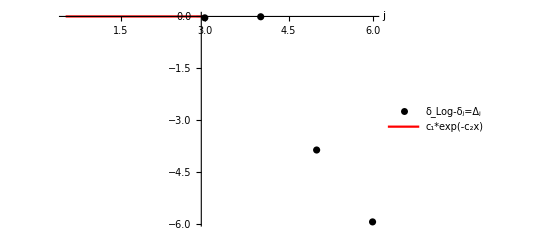

```mathematica
Show[
ListPlot[dadosFeigenbaum, AxesLabel->{"j"},PlotStyle->{Black},PlotLegends->{"δ_Log-δ_j=Δ_j"}],
Plot[aux[x]/.{ajusteFeigenbaum["BestFitParameters"][[1]],ajusteFeigenbaum["BestFitParameters"][[2]]},
{x,0,3},PlotStyle->{Red},PlotLegends->{"c_1*exp(-c_2x)"}],
PlotRange->All

]
```

```mathematica
(*Exercício 6*)
(*Começo definindo a função que calcula os coeficientes de Lyapunov*)
lyapunovC=Compile[{a,x0,{n,_Integer},{m,_Integer}},
xlista=Drop[NestList[a*Sin[π*#]&,x0,n],m+1];
Total[Log[Abs[π*a*Cos[π*xlista]]]]/Length[xlista]
];
```

```mathematica
(*No caso em que a = 1 :*)
lyapunovC[1,0.5,10000,100]
```

0.689608

```mathematica
(* Faço novos testes com quantidades de iteração maiores para verificar a convergência do resultado *)
lyapunovC[1,0.5,100000,100]
lyapunovC[1,0.5,1000000,100]
lyapunovC[1,0.5,10000000,100]
```

0.688815

0.689004

0.689119

```mathematica
(*Concluimos então que, para o valor do parâmetro a sendo igual a 1, o expoente de Lyapunov com 3 algarismos significativos é 0.689*)
```

```mathematica
(*Plot do expoente de Lyapunov para 0.5 < a < 1*)
Plot[lyapunovC[a,0.5,10000,1000],{a,0.5,1},Evaluate[optam],AxesLabel-> {"a","Expoente de Lyapunov"}]
```

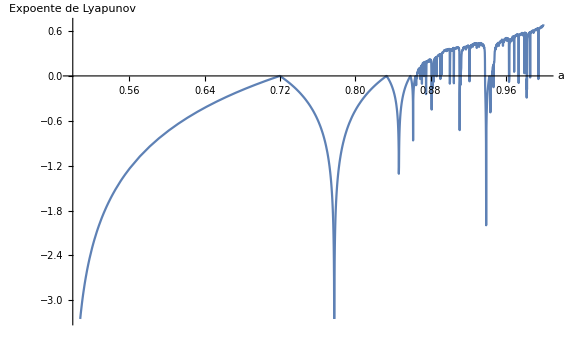

```mathematica
(*O mapa passa a exibir comportamento caótico a partir de a = 0.85, aproximadamente, pois é justamente nessa região que as ilhas de estabilidade se tornam muito mais frequentes. Para verificar essa hipótese, construo um novo gráfico focalizado dentro dessa região específica.*)
```

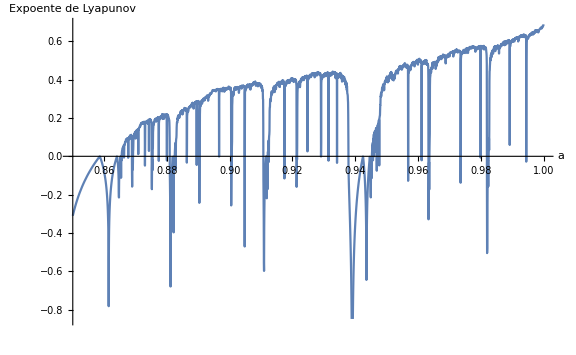

```mathematica
Plot[lyapunovC[a,0.5,10000,1000],{a,0.85,1},Evaluate[optam],AxesLabel-> {"a","Expoente de Lyapunov"}]
```